# nearest neighbor algorithm

параллельная доставка дронов
матрица расстояний

## входные данные

### поле:

```mathematica
rows=400;
columns=600;
```

### дроны:

```mathematica
numberOfDrones=5;
turnsOfDrones=100000;
capacityOfDrones = 200;
```

### продукты:

```mathematica
numberOfProducts=5;
productsWeights = RandomInteger[{1,capacityOfDrones},numberOfProducts];
maxNumberOfProductsInWarehouses=7000;
```

### склады:

```mathematica
numberOfWarehouses = 4;
```

```mathematica
Clear@generateWarehousesCoords
generateWarehousesCoords[rows_Integer,columns_Integer,number_Integer]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
warehousesCoords=generateWarehousesCoords[rows,columns,numberOfWarehouses]
```

{{466,357},{66,101},{196,190},{372,211}}

```mathematica
productsInWarehouses=RandomInteger[maxNumberOfProductsInWarehouses,{numberOfWarehouses,numberOfProducts}];
```

```mathematica
totalNumberOfProducts=Total@productsInWarehouses
```

{9452,13144,17036,10721,13792}

### заказы:

```mathematica
numberOfOrders =20;
```

```mathematica
Clear@generateOrdersCoords
generateOrdersCoords[rows_Integer,columns_Integer,number_Integer,warehouses:{{_Integer,_Integer}..}]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords~Join~warehousesCoords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
ordersCoords=generateOrdersCoords[rows,columns,numberOfOrders,warehousesCoords];
```

```mathematica
Floor[Mean@totalNumberOfProducts/numberOfOrders]
```

641

```mathematica
Clear@generateOrders
generateOrders[numberOfOrders_Integer,totalNumberOfProducts_List]:=
({1}~Join~ConstantArray[0,numberOfProducts-1])+#&/@RandomInteger[
Min[Floor[Mean@totalNumberOfProducts/numberOfOrders],2],
{numberOfOrders,Length@totalNumberOfProducts}
]
```

```mathematica
orders=generateOrders[numberOfOrders,totalNumberOfProducts];
```

### база данных

```mathematica
d=Ceiling@DistanceMatrix@Join[warehousesCoords,ordersCoords];
```

```mathematica
data=<|
"general"-> <|
"rows"->rows,
"columns"->columns,
"turns"-> turnsOfDrones,
"capacity"-> capacityOfDrones,
"numberOfDrones"->numberOfDrones,
"numberOfProducts"->numberOfProducts,
"numberOfWarehouses"-> numberOfWarehouses,
"numberOfOrders"-> numberOfOrders,
"weightsOfProducts"->productsWeights
|>,

"drones"->AssociationThread[Range@numberOfDrones->(<|"position"->1,"products"->#⟦2⟧,"score"->#⟦3⟧|>&/@Thread[{ConstantArray[warehousesCoords⟦1⟧,numberOfDrones],ConstantArray[0,{numberOfDrones,numberOfProducts}],ConstantArray[0,numberOfDrones]}])]~Join~
<|"mask"-> ConstantArray[False,numberOfDrones]|>,

"warehouses"->AssociationThread[Range@numberOfWarehouses->(<|"products"->#⟦2⟧|>&/@Thread[{warehousesCoords,productsInWarehouses}])],

"orders"-><|
"order"->AssociationThread[Range@numberOfOrders->(<|"list"->#⟦2⟧,"turns"-> 0|>&/@Thread[{ordersCoords,orders}])],
"mask"->ConstantArray[0,numberOfOrders],
"done"->False
|>,
"dMatrix"-><|"w"->Transpose@d⟦;;numberOfWarehouses⟧,
"o"->d⟦;;numberOfWarehouses,numberOfWarehouses+1;;⟧|>
|>;
```

```mathematica
data
```

<|general→<|rows→400,columns→600,turns→100000,capacity→200,numberOfDrones→5,numberOfProducts→5,numberOfWarehouses→4,numberOfOrders→20,weightsOfProducts→{64,34,171,108,177}|>,drones→<|1→<|position→1,products→{0,0,0,0,0},score→0|>,2→<|position→1,products→{0,0,0,0,0},score→0|>,3→<|position→1,products→{0,0,0,0,0},score→0|>,4→<|position→1,products→{0,0,0,0,0},score→0|>,5→<|position→1,products→{0,0,0,0,0},score→0|>,mask→{False,False,False,False,False}|>,warehouses→<|1→<|products→{1222,280,475,2604,3846}|>,2→<|products→{4051,2340,5884,1374,1938}|>,3→<|products→{3854,6138,4816,525,5820}|>,4→<|products→{325,4386,5861,6218,2188}|>|>,orders→<|order→<|1→<|list→{1,2,2,1,0},turns→0|>,2→<|list→{1,1,0,0,1},turns→0|>,3→<|list→{1,0,1,1,0},turns→0|>,4→<|list→{2,1,2,1,0},turns→0|>,5→<|list→{3,2,2,2,1},turns→0|>,6→<|list→{1,0,2,2,2},turns→0|>,7→<|list→{3,2,2,0,0},turns→0|>,8→<|list→{1,0,2,2,1},turns→0|>,9→<|list→{3,1,0,0,0},turns→0|>,10→<|list→{2,1,1,2,2},turns→0|>,11→<|list→{2,2,0,1,2},turns→0|>,12→<|list→{3,0,2,1,2},turns→0|>,13→<|list→{2,0,0,0,1},turns→0|>,14→<|list→{2,1,1,1,1},turns→0|>,15→<|list→{2,1,1,2,1},turns→0|>,16→<|list→{3,2,0,2,1},turns→0|>,17→<|list→{2,0,1,0,2},turns→0|>,18→<|list→{3,2,1,0,1},turns→0|>,19→<|list→{2,2,0,1,0},turns→0|>,20→<|list→{1,2,0,2,1},turns→0|>|>,mask→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},done→False|>,dMatrix→<|w→{{0,475,318,174},{475,0,158,326},{318,158,0,178},{174,326,178,0},{118,370,213,128},{402,147,138,231},{208,486,352,181},{93,431,279,107},{412,254,217,348},{164,458,318,142},{120,368,211,127},{229,302,165,193},{314,176,61,152},{318,224,134,144},{195,340,197,189},{371,115,71,213},{323,160,44,166},{402,281,232,351},{421,92,123,257},{451,63,140,317},{391,88,78,238},{364,183,132,191},{350,131,41,217},{516,73,203,379}},o→{{118,402,208,93,412,164,120,229,314,318,195,371,323,402,421,451,391,364,350,516},{370,147,486,431,254,458,368,302,176,224,340,115,160,281,92,63,88,183,131,73},{213,138,352,279,217,318,211,165,61,134,197,71,44,232,123,140,78,132,41,203},{128,231,181,107,348,142,127,193,152,144,189,213,166,351,257,317,238,191,217,379}}|>|>

## анализ данных

```mathematica
plot=ListPlot[{MapThread[Labeled,{Values@data⟦"warehouses",All,"coords"⟧,Range@data["general","numberOfWarehouses"]}],MapThread[Labeled,{Values@data⟦"orders","order",All,"coords"⟧,
Range@data["general","numberOfOrders"]}]},PlotTheme->"Detailed",PlotStyle->{PointSize[0.03],PointSize[0.02]}]
```

-Graphics-

## алгоритм

на каждой итерации параллельно посылаем дронов на заказы (несколько дронов могут выбрать один заказ и закрыть его за один ход), при этом бронируя продукты.

```mathematica
plot
```

-Graphics-

```mathematica
solution
```

<|general→<|rows→400,7,weightsOfProducts→{73,40,84,107,52,36,13,74,36,94,93,46,123,24,100,93,62,49,97,102,80,37,22,25,72,48,40,74,32,31,136,64,99,37,44,36,104,74,112,40,65,67,50,143,23,26,91,20,142,128,9,77,40,26,55,104,59,112,42,69,87,89,2,11,105,43,105,23,21,88,57,40,52,63,35,141,54,27,45,37,21,37,102,38,36,117,57,226,33,58,130,41,34,33,62,129,79,103,104,56,33,118,96,21,18,65,140,87,91,61,54,137,71,84,35,75,32,4,68,37,80,78,91,75,52,74,96,32,85,42,78,119,58,16,44,24,98,121,76,16,56,112,67,58,46,76,45,41,94,55,44,51,136,63,34,86,87,64,54,27,69,31,64,138,56,97,81,40,132,64,114,105,41,52,60}|>,4,i→1250|>
 |  |  |  |

```mathematica
Clear@loadProducts
loadProducts[data_Association,warehouseID_Integer,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data,capacity =data["general","capacity"],weights=data["general","weightsOfProducts"],numberOfProduct},
Do[
numberOfProduct=
Min[
data⟦"warehouses",warehouseID,"products",i⟧,
data⟦"orders","order",orderID,"list",i⟧,
Quotient[capacity,weights⟦i⟧]
];
tempData⟦"warehouses",warehouseID,"products",i⟧-=numberOfProduct;
tempData⟦"drones",droneID,"products",i⟧+=numberOfProduct;
capacity-=weights⟦i⟧ numberOfProduct;

(*If[numberOfProduct>0,
Print["дрон ",droneID," загрузил ",numberOfProduct, " у.е. продукта ", i, " со склада ",warehouseID," для заказа ", orderID]];*)

If[capacity≤0,
Break[]
]

,{i,Length@weights}];
tempData
]
```

```mathematica
Clear@calculateTurns
calculateTurns[turn_Integer,data_Association]:=
With[{T=data["general","turns"]},Ceiling[(T-turn)/T 100]]
```

```mathematica
Clear@unloadProduct
unloadProduct[data_Association,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data},
tempData⟦"orders","order",orderID,"list"⟧-=tempData⟦"drones",droneID,"products"⟧;
tempData⟦"drones",droneID,"products"⟧=ConstantArray[0,data["general","numberOfProducts"]];

If[
Total@tempData⟦"orders","order",orderID,"list"⟧==0,

tempData⟦"orders","mask",orderID⟧=1;
tempData["orders","order",orderID,"turns"]=calculateTurns[data["drones",droneID,"score"],tempData];
If[
Total@tempData⟦"orders","mask"⟧==tempData["general","numberOfOrders"],tempData["orders","done"]=True
]

(*tempData["i"]+=1;
Print[tempData["i"]*)
];
tempData
]
```

```mathematica
Clear@chooseNextDirection
chooseNextDirection[droneID_,data_Association]:=
Module[
{warehouses,warehouse,order={},orderCoords,tempData=data,score},

If[
!(tempData⟦"drones","mask",droneID⟧∨tempData["orders","done"]),
(*выбор ближайшего склада, где есть хотя бы один продукт*)
warehouses=SortBy[
Keys@
Select[
tempData⟦"warehouses"⟧,
Total@#["products"]≠0&
]⟦All,"coords"⟧,
tempData⟦"dMatrix","w",tempData["drones",droneID,"position"],#⟧&];

(*определяем ближайший заказ*)
Do[
order=First[
SortBy[
Keys@Select[
Pick[data⟦"orders","order",All⟧,data["orders","mask"],0],Composition[#>0&,Total,Times[data["warehouses",warehouseLocal,"products"],#["list"]]&]
],
data⟦"dMatrix","o",warehouseLocal,#⟧&
],
{}];
If[order=!={},
warehouse=warehouseLocal;
Break[]],
{warehouseLocal,warehouses}];

(*"бронируем" продукты, то есть сразу же загружаем*)
score=tempData⟦"dMatrix","w",tempData["drones",droneID,"position"],warehouse⟧+tempData⟦"dMatrix","o",warehouse,order⟧+2;

If[
tempData["drones",droneID,"score"]+score≥tempData["general","turns"],
tempData⟦"drones","mask",droneID⟧=True;
Return[tempData]
];


(*Print["drone ",droneID," order ", order];*)

tempData=loadProducts[tempData,warehouse,order,droneID];

tempData["drones",droneID,"position"]=order;
tempData["drones",droneID,"score"]+=score;


(*разгружаем*)
unloadProduct[tempData,order,droneID],
tempData
]
]
```

```mathematica
Clear@solve
solve[data_Association]:=
Module[
{tempData=data},
If[!And@@(#≥0&/@(Total@Values@data⟦"warehouses",All,"products"⟧-Total@Values@data⟦"orders","order",All,"list"⟧)),
Print["недостаточно продуктов на складах"];Return[{}]
];
While[
!tempData["orders","done"],
If[
And@@tempData["drones","mask"],
Print["не хватило ходов"];
Return[tempData]
];

Do[
tempData=chooseNextDirection[i,tempData]
,{i,tempData["general","numberOfDrones"]}
]
];
tempData
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
data=<<"data_dict";
solution=<<"solution_by_2_3_1";
```

C:\Users\rpd13\python repositories\kaggle_drones\nearest neighbor

```mathematica
data["i"]=0
```

0

18:40

```mathematica
solution=solve[data]
```

<|general→<|rows→400,columns→600,turns→100000,capacity→200,numberOfDrones→5,numberOfProducts→5,numberOfWarehouses→4,numberOfOrders→20,weightsOfProducts→{64,34,171,108,177}|>,drones→<|1→<|position→5,products→{0,0,0,0,0},score→4043|>,2→<|position→5,products→{0,0,0,0,0},score→4404|>,3→<|position→5,products→{0,0,0,0,0},score→4224|>,4→<|position→5,products→{0,0,0,0,0},score→3281|>,5→<|position→5,products→{0,0,0,0,0},score→4206|>,mask→{False,False,False,False,False}|>,warehouses→<|1→<|products→{1216,276,469,2600,3840}|>,2→<|products→{4047,2336,5883,1371,1936}|>,3→<|products→{3833,6129,4809,517,5812}|>,4→<|products→{316,4381,5855,6212,2185}|>|>,orders→<|order→<|1→<|list→{0,0,0,0,0},turns→100|>,2→<|list→{0,0,0,0,0},turns→98|>,3→<|list→{0,0,0,0,0},turns→98|>,4→<|list→{0,0,0,0,0},turns→100|>,5→<|list→{0,0,0,0,0},turns→96|>,6→<|list→{0,0,0,0,0},turns→99|>,7→<|list→{0,0,0,0,0},turns→100|>,8→<|list→{0,0,0,0,0},turns→97|>,9→<|list→{0,0,0,0,0},turns→100|>,10→<|list→{0,0,0,0,0},turns→98|>,11→<|list→{0,0,0,0,0},turns→98|>,12→<|list→{0,0,0,0,0},turns→99|>,13→<|list→{0,0,0,0,0},turns→100|>,14→<|list→{0,0,0,0,0},turns→96|>,15→<|list→{0,0,0,0,0},turns→99|>,16→<|list→{0,0,0,0,0},turns→98|>,17→<|list→{0,0,0,0,0},turns→99|>,18→<|list→{0,0,0,0,0},turns→98|>,19→<|list→{0,0,0,0,0},turns→100|>,20→<|list→{0,0,0,0,0},turns→98|>|>,mask→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},done→True|>,dMatrix→<|w→{{0,475,318,174},{475,0,158,326},{318,158,0,178},{174,326,178,0},{118,370,213,128},{402,147,138,231},{208,486,352,181},{93,431,279,107},{412,254,217,348},{164,458,318,142},{120,368,211,127},{229,302,165,193},{314,176,61,152},{318,224,134,144},{195,340,197,189},{371,115,71,213},{323,160,44,166},{402,281,232,351},{421,92,123,257},{451,63,140,317},{391,88,78,238},{364,183,132,191},{350,131,41,217},{516,73,203,379}},o→{{118,402,208,93,412,164,120,229,314,318,195,371,323,402,421,451,391,364,350,516},{370,147,486,431,254,458,368,302,176,224,340,115,160,281,92,63,88,183,131,73},{213,138,352,279,217,318,211,165,61,134,197,71,44,232,123,140,78,132,41,203},{128,231,181,107,348,142,127,193,152,144,189,213,166,351,257,317,238,191,217,379}}|>|>

```mathematica
Table[
solution⟦"drones",i,"score"⟧,{i,30}]
```

{51019,51324,51504,52573,50118,50529,53505,51729,51313,51540,50771,54305,52433,51003,49823,49475,53287,51501,52454,51005,51880,51139,49482,51409,51716,53196,50220,52264,52039,53812}

```mathematica
solution["drones","mask"]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Total@Values@data⟦"orders","order",All,"list"⟧==(Total@Values@data⟦"warehouses",All,"products"⟧-Total@Values@solution⟦"warehouses",All,"products"⟧)
```

True

```mathematica
Total@Values@data⟦"orders","order",All,"list"⟧;
```

```mathematica
Values@solution⟦"warehouses",All,"products"⟧;
```

```mathematica
SortBy[solution⟦"orders","order",All,"turns"⟧,Value]
N@Mean@Values@%
N@StandardDeviation@Values@%%
Total@Values@%%%
```

<|1055→52,99→53,348→53,424→53,707→53,1016→53,1107→53,49→54,183→54,289→54,514→54,605→54,624→54,897→54,1142→54,1224→54,71→55,100→55,126→55,214→55,226→55,290→55,317→55,336→55,504→55,506→55,527→55,547→55,570→55,583→55,598→55,620→55,648→55,756→55,797→55,816→55,856→55,892→55,1031→55,1103→55,1130→55,1166→55,1168→55,35→56,171→56,179→56,192→56,254→56,259→56,315→56,363→56,377→56,396→56,452→56,491→56,492→56,575→56,582→56,602→56,693→56,700→56,701→56,714→56,736→56,738→56,742→56,784→56,806→56,837→56,858→56,881→56,885→56,921→56,938→56,943→56,948→56,964→56,976→56,1086→56,1091→56,1100→56,1112→56,1131→56,1145→56,1218→56,1242→56,9→57,17→57,43→57,57→57,64→57,104→57,140→57,167→57,218→57,278→57,286→57,307→57,311→57,326→57,361→57,365→57,368→57,389→57,398→57,407→57,434→57,448→57,449→57,460→57,469→57,471→57,482→57,539→57,554→57,567→57,590→57,718→57,754→57,786→57,808→57,848→57,875→57,903→57,946→57,1015→57,1041→57,1048→57,1064→57,1071→57,1105→57,1108→57,1128→57,1139→57,1199→57,1248→57,25→58,34→58,41→58,66→58,73→58,77→58,101→58,135→58,174→58,190→58,201→58,209→58,212→58,257→58,265→58,267→58,342→58,399→58,436→58,445→58,459→58,470→58,501→58,548→58,586→58,594→58,601→58,627→58,659→58,663→58,721→58,745→58,750→58,764→58,780→58,814→58,818→58,840→58,901→58,905→58,967→58,1009→58,1040→58,1111→58,1126→58,1167→58,1179→58,1193→58,1198→58,1206→58,1210→58,40→59,62→59,130→59,133→59,149→59,160→59,165→59,169→59,216→59,230→59,231→59,281→59,321→59,330→59,331→59,340→59,356→59,411→59,433→59,458→59,487→59,489→59,524→59,537→59,577→59,589→59,617→59,626→59,632→59,670→59,682→59,724→59,741→59,763→59,775→59,833→59,850→59,855→59,872→59,880→59,900→59,915→59,1012→59,1045→59,1075→59,1077→59,1209→59,1229→59,13→60,55→60,89→60,94→60,103→60,105→60,123→60,136→60,176→60,193→60,197→60,203→60,232→60,234→60,247→60,291→60,293→60,297→60,298→60,325→60,374→60,382→60,386→60,402→60,430→60,432→60,468→60,493→60,631→60,654→60,666→60,691→60,699→60,710→60,733→60,735→60,737→60,798→60,800→60,804→60,821→60,843→60,863→60,877→60,950→60,958→60,993→60,998→60,1014→60,1029→60,1032→60,1058→60,1074→60,1076→60,1113→60,1114→60,1149→60,1155→60,1170→60,1174→60,1190→60,1228→60,15→61,33→61,74→61,96→61,111→61,115→61,134→61,148→61,154→61,161→61,199→61,233→61,268→61,294→61,335→61,343→61,344→61,404→61,409→61,472→61,480→61,483→61,495→61,496→61,512→61,549→61,576→61,612→61,642→61,646→61,649→61,715→61,774→61,778→61,789→61,820→61,834→61,839→61,883→61,907→61,942→61,978→61,992→61,1006→61,1030→61,1053→61,1079→61,1095→61,1102→61,1121→61,1140→61,1178→61,1201→61,1203→61,1215→61,38→62,86→62,170→62,205→62,242→62,251→62,252→62,263→62,271→62,285→62,299→62,300→62,305→62,359→62,387→62,412→62,420→62,425→62,437→62,585→62,609→62,610→62,614→62,669→62,698→62,711→62,726→62,731→62,760→62,783→62,827→62,847→62,870→62,891→62,944→62,963→62,966→62,988→62,989→62,1011→62,1018→62,1020→62,1028→62,1039→62,1068→62,1127→62,1132→62,1138→62,1154→62,1156→62,1159→62,1173→62,1188→62,1241→62,6→63,14→63,82→63,95→63,118→63,137→63,185→63,191→63,206→63,222→63,227→63,279→63,312→63,351→63,400→63,403→63,405→63,414→63,415→63,431→63,441→63,443→63,477→63,536→63,565→63,578→63,641→63,645→63,683→63,694→63,708→63,719→63,751→63,773→63,845→63,874→63,895→63,898→63,970→63,984→63,987→63,1001→63,1027→63,1037→63,1044→63,1153→63,1165→63,1189→63,1191→63,1211→63,1230→63,1250→63,5→64,11→64,22→64,39→64,42→64,91→64,108→64,141→64,150→64,220→64,229→64,244→64,301→64,395→64,406→64,451→64,475→64,497→64,511→64,529→64,543→64,553→64,611→64,634→64,650→64,660→64,686→64,687→64,703→64,725→64,753→64,794→64,802→64,852→64,860→64,868→64,887→64,953→64,1007→64,1093→64,1101→64,1176→64,1195→64,52→65,56→65,156→65,189→65,198→65,270→65,273→65,282→65,341→65,373→65,381→65,401→65,457→65,499→65,522→65,523→65,566→65,599→65,600→65,629→65,639→65,661→65,696→65,697→65,713→65,723→65,729→65,765→65,825→65,857→65,934→65,955→65,1000→65,1036→65,1043→65,1106→65,1182→65,1186→65,1219→65,7→66,46→66,63→66,81→66,90→66,125→66,127→66,131→66,200→66,202→66,269→66,274→66,280→66,283→66,333→66,390→66,455→66,474→66,533→66,551→66,568→66,676→66,680→66,705→66,722→66,770→66,811→66,812→66,822→66,846→66,859→66,876→66,906→66,925→66,928→66,968→66,1026→66,1070→66,1122→66,1226→66,28→67,59→67,61→67,67→67,69→67,110→67,112→67,266→67,309→67,349→67,362→67,408→67,435→67,439→67,462→67,516→67,520→67,525→67,526→67,542→67,597→67,618→67,668→67,672→67,674→67,720→67,894→67,911→67,949→67,986→67,1003→67,1046→67,1057→67,1096→67,1136→67,1225→67,1247→67,45→68,60→68,83→68,102→68,106→68,187→68,217→68,236→68,249→68,316→68,323→68,345→68,360→68,440→68,490→68,531→68,534→68,555→68,557→68,563→68,593→68,603→68,622→68,647→68,657→68,677→68,704→68,766→68,767→68,785→68,792→68,826→68,828→68,842→68,899→68,916→68,941→68,959→68,979→68,995→68,1042→68,1090→68,1208→68,29→69,129→69,146→69,177→69,195→69,253→69,255→69,338→69,358→69,545→69,584→69,655→69,688→69,747→69,782→69,867→69,902→69,918→69,919→69,924→69,956→69,1034→69,1049→69,1060→69,1063→69,1067→69,1115→69,1133→69,1180→69,1240→69,16→70,53→70,65→70,72→70,248→70,262→70,423→70,442→70,467→70,519→70,556→70,579→70,615→70,616→70,644→70,675→70,831→70,866→70,908→70,912→70,913→70,975→70,1022→70,1033→70,1157→70,1197→70,1221→70,1244→70,21→71,24→71,76→71,93→71,163→71,211→71,243→71,337→71,352→71,392→71,421→71,446→71,498→71,515→71,571→71,606→71,619→71,695→71,727→71,748→71,759→71,819→71,841→71,869→71,933→71,1017→71,1024→71,1052→71,1161→71,1164→71,1175→71,1217→71,1238→71,26→72,75→72,97→72,119→72,132→72,162→72,184→72,223→72,241→72,245→72,417→72,422→72,461→72,532→72,535→72,540→72,546→72,580→72,596→72,671→72,743→72,758→72,815→72,832→72,849→72,923→72,1050→72,1069→72,1080→72,1083→72,1092→72,1143→72,1171→72,1194→72,1214→72,1233→72,1245→72,87→73,120→73,173→73,272→73,366→73,371→73,581→73,613→73,667→73,685→73,690→73,734→73,757→73,873→73,910→73,1118→73,1147→73,1237→73,1→74,58→74,79→74,158→74,166→74,175→74,295→74,319→74,328→74,375→74,503→74,538→74,558→74,587→74,608→74,749→74,829→74,982→74,1004→74,1087→74,1089→74,1097→74,1099→74,1141→74,1172→74,116→75,139→75,196→75,235→75,239→75,318→75,413→75,419→75,429→75,473→75,484→75,777→75,844→75,851→75,864→75,865→75,893→75,935→75,947→75,954→75,969→75,1062→75,1078→75,1084→75,1151→75,1181→75,23→76,114→76,142→76,275→76,277→76,324→76,329→76,438→76,479→76,510→76,517→76,591→76,623→76,744→76,796→76,799→76,803→76,961→76,985→76,997→76,1061→76,1124→76,1148→76,1162→76,1163→76,1222→76,31→77,153→77,308→77,314→77,327→77,355→77,369→77,416→77,428→77,509→77,572→77,573→77,630→77,681→77,762→77,904→77,927→77,929→77,936→77,977→77,1002→77,1051→77,1137→77,1160→77,1213→77,1227→77,30→78,70→78,85→78,159→78,237→78,238→78,347→78,388→78,397→78,427→78,476→78,541→78,569→78,592→78,638→78,656→78,673→78,702→78,787→78,838→78,952→78,983→78,1005→78,1038→78,1066→78,1117→78,1119→78,1146→78,1249→78,68→79,98→79,107→79,113→79,228→79,292→79,306→79,380→79,391→79,418→79,481→79,882→79,888→79,999→79,1010→79,1023→79,1098→79,1109→79,48→80,122→80,151→80,152→80,224→80,225→80,264→80,296→80,372→80,453→80,500→80,559→80,560→80,712→80,861→80,878→80,1183→80,1185→80,4→81,92→81,188→81,302→81,376→81,444→81,633→81,635→81,662→81,791→81,793→81,795→81,810→81,1082→81,1110→81,1220→81,109→82,143→82,260→82,284→82,320→82,334→82,353→82,394→82,456→82,485→82,494→82,508→82,550→82,561→82,564→82,739→82,790→82,823→82,1088→82,1123→82,1158→82,1205→82,1232→82,1246→82,27→83,50→83,80→83,172→83,186→83,215→83,246→83,261→83,370→83,384→83,447→83,530→83,625→83,709→83,776→83,781→83,807→83,836→83,917→83,922→83,932→83,960→83,972→83,1008→83,1125→83,1169→83,1207→83,1236→83,1239→83,18→84,117→84,128→84,164→84,178→84,213→84,313→84,332→84,346→84,450→84,588→84,607→84,651→84,692→84,768→84,1150→84,1223→84,10→85,20→85,36→85,37→85,144→85,204→85,486→85,528→85,604→85,621→85,637→85,640→85,652→85,771→85,813→85,835→85,889→85,945→85,965→85,1035→85,1192→85,1202→85,182→86,466→86,488→86,507→86,684→86,717→86,879→86,930→86,973→86,994→86,1072→86,1085→86,1116→86,84→87,124→87,145→87,180→87,716→87,1025→87,1094→87,1144→87,1177→87,1212→87,44→88,78→88,219→88,221→88,258→88,303→88,322→88,367→88,505→88,518→88,643→88,653→88,706→88,772→88,886→88,1081→88,1187→88,8→89,250→89,379→89,385→89,521→89,562→89,761→89,769→89,817→89,991→89,1019→89,1184→89,1231→89,88→90,210→90,256→90,678→90,740→90,779→90,1047→90,1120→90,1152→90,2→91,19→91,47→91,168→91,288→91,378→91,809→91,1134→91,1235→91,54→92,155→92,181→92,513→92,689→92,957→92,32→93,121→93,138→93,147→93,194→93,310→93,354→93,357→93,454→93,463→93,730→93,746→93,824→93,896→93,951→93,1073→93,207→94,478→94,628→94,679→94,752→94,871→94,971→94,974→94,1013→94,1065→94,1234→94,208→95,339→95,464→95,502→95,732→95,755→95,890→95,996→95,1059→95,240→96,304→96,393→96,658→96,788→96,931→96,940→96,981→96,1196→96,287→97,664→97,728→97,854→97,1204→97,1243→97,51→98,276→98,574→98,595→98,853→98,884→98,920→98,980→98,1054→98,1056→98,1129→98,157→99,350→99,465→99,544→99,552→99,805→99,939→99,3→100,12→100,364→100,383→100,410→100,426→100,636→100,665→100,801→100,830→100,862→100,909→100,914→100,926→100,937→100,962→100,990→100,1021→100,1104→100,1135→100,1200→100,1216→100|>

70.6048

11.9963

88256

```mathematica
114269/1250//N
```

91.4152

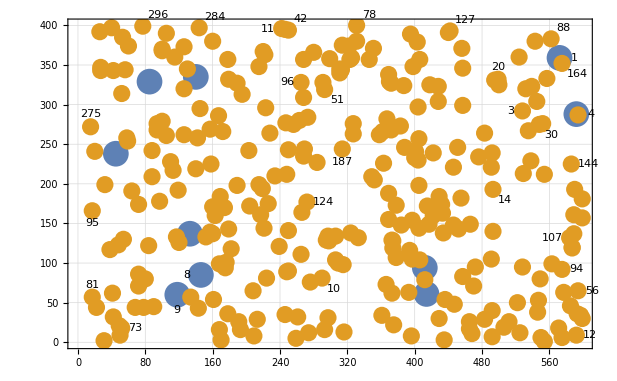

```mathematica
plot
```

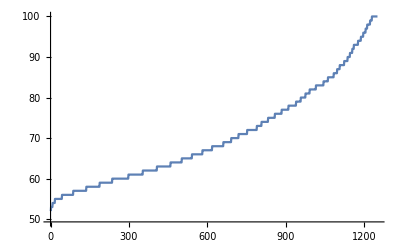

```mathematica
ListLinePlot@Values@SortBy[solution⟦"orders","order",All,"turns"⟧,Value]
```